# Graph Analysis

#### x

```mathematica
provinces=Entity["Country","China"][EntityProperty["Country","AdministrativeDivisions"]]
```

{Anhui, China,Beijing, China,Chongqing, China,Fujian, China,Gansu, China,Guangdong, China,Guangxi, China,Guizhou, China,Hainan, China,Hebei, China,Heilongjiang, China,Henan, China,Hubei, China,Hunan, China,Jiangsu, China,Jiangxi, China,Jilin, China,Liaoning, China,Neimenggu, China,Ningxia, China,Qinghai, China,Shaanxi, China,Shandong, China,Shanghai, China,Shanxi, China,Sichuan, China,Tianjin, China,Xinjiang, China,Xizang, China,Yunnan, China,Zhejiang, China}

```mathematica
g={Entity["AdministrativeDivision",{"Anhui","China"}]<->Entity["AdministrativeDivision",{"Henan","China"}],Entity["AdministrativeDivision",{"Anhui","China"}]<->Entity["AdministrativeDivision",{"Hubei","China"}],Entity["AdministrativeDivision",{"Anhui","China"}]<->Entity["AdministrativeDivision",{"Jiangxi","China"}],Entity["AdministrativeDivision",{"Beijing","China"}]<->Entity["AdministrativeDivision",{"Tianjin","China"}],Entity["AdministrativeDivision",{"Chongqing","China"}]<->Entity["AdministrativeDivision",{"Guizhou","China"}],Entity["AdministrativeDivision",{"Chongqing","China"}]<->Entity["AdministrativeDivision",{"Hubei","China"}],Entity["AdministrativeDivision",{"Chongqing","China"}]<->Entity["AdministrativeDivision",{"Hunan","China"}],Entity["AdministrativeDivision",{"Chongqing","China"}]<->Entity["AdministrativeDivision",{"Shaanxi","China"}],Entity["AdministrativeDivision",{"Chongqing","China"}]<->Entity["AdministrativeDivision",{"Sichuan","China"}],Entity["AdministrativeDivision",{"Fujian","China"}]<->Entity["AdministrativeDivision",{"Jiangxi","China"}],Entity["AdministrativeDivision",{"Fujian","China"}]<->Entity["AdministrativeDivision",{"Zhejiang","China"}],Entity["AdministrativeDivision",{"Gansu","China"}]<->Entity["AdministrativeDivision",{"Neimenggu","China"}],Entity["AdministrativeDivision",{"Gansu","China"}]<->Entity["AdministrativeDivision",{"Ningxia","China"}],Entity["AdministrativeDivision",{"Gansu","China"}]<->Entity["AdministrativeDivision",{"Shaanxi","China"}],Entity["AdministrativeDivision",{"Gansu","China"}]<->Entity["AdministrativeDivision",{"Sichuan","China"}],Entity["AdministrativeDivision",{"Guangdong","China"}]<->Entity["AdministrativeDivision",{"Fujian","China"}],Entity["AdministrativeDivision",{"Guangdong","China"}]<->Entity["AdministrativeDivision",{"Hainan","China"}],Entity["AdministrativeDivision",{"Guangdong","China"}]<->Entity["AdministrativeDivision",{"Hunan","China"}],Entity["AdministrativeDivision",{"Guangdong","China"}]<->Entity["AdministrativeDivision",{"Jiangxi","China"}],Entity["AdministrativeDivision",{"Guangxi","China"}]<->Entity["AdministrativeDivision",{"Guangdong","China"}],Entity["AdministrativeDivision",{"Guangxi","China"}]<->Entity["AdministrativeDivision",{"Guizhou","China"}],Entity["AdministrativeDivision",{"Guangxi","China"}]<->Entity["AdministrativeDivision",{"Hunan","China"}],Entity["AdministrativeDivision",{"Guizhou","China"}]<->Entity["AdministrativeDivision",{"Hunan","China"}],Entity["AdministrativeDivision",{"Guizhou","China"}]<->Entity["AdministrativeDivision",{"Sichuan","China"}],Entity["AdministrativeDivision",{"Hebei","China"}]<->Entity["AdministrativeDivision",{"Beijing","China"}],Entity["AdministrativeDivision",{"Hebei","China"}]<->Entity["AdministrativeDivision",{"Henan","China"}],Entity["AdministrativeDivision",{"Hebei","China"}]<->Entity["AdministrativeDivision",{"Liaoning","China"}],Entity["AdministrativeDivision",{"Hebei","China"}]<->Entity["AdministrativeDivision",{"Neimenggu","China"}],Entity["AdministrativeDivision",{"Hebei","China"}]<->Entity["AdministrativeDivision",{"Shanxi","China"}],Entity["AdministrativeDivision",{"Hebei","China"}]<->Entity["AdministrativeDivision",{"Tianjin","China"}],Entity["AdministrativeDivision",{"Heilongjiang","China"}]<->Entity["AdministrativeDivision",{"Neimenggu","China"}],Entity["AdministrativeDivision",{"Henan","China"}]<->Entity["AdministrativeDivision",{"Hubei","China"}],Entity["AdministrativeDivision",{"Henan","China"}]<->Entity["AdministrativeDivision",{"Shaanxi","China"}],Entity["AdministrativeDivision",{"Henan","China"}]<->Entity["AdministrativeDivision",{"Shanxi","China"}],Entity["AdministrativeDivision",{"Hubei","China"}]<->Entity["AdministrativeDivision",{"Hunan","China"}],Entity["AdministrativeDivision",{"Hubei","China"}]<->Entity["AdministrativeDivision",{"Shaanxi","China"}],Entity["AdministrativeDivision",{"Jiangsu","China"}]<->Entity["AdministrativeDivision",{"Anhui","China"}],Entity["AdministrativeDivision",{"Jiangsu","China"}]<->Entity["AdministrativeDivision",{"Shandong","China"}],Entity["AdministrativeDivision",{"Jiangxi","China"}]<->Entity["AdministrativeDivision",{"Hubei","China"}],Entity["AdministrativeDivision",{"Jiangxi","China"}]<->Entity["AdministrativeDivision",{"Hunan","China"}],Entity["AdministrativeDivision",{"Jilin","China"}]<->Entity["AdministrativeDivision",{"Heilongjiang","China"}],Entity["AdministrativeDivision",{"Jilin","China"}]<->Entity["AdministrativeDivision",{"Neimenggu","China"}],Entity["AdministrativeDivision",{"Liaoning","China"}]<->Entity["AdministrativeDivision",{"Jilin","China"}],Entity["AdministrativeDivision",{"Liaoning","China"}]<->Entity["AdministrativeDivision",{"Neimenggu","China"}],Entity["AdministrativeDivision",{"Ningxia","China"}]<->Entity["AdministrativeDivision",{"Neimenggu","China"}],Entity["AdministrativeDivision",{"Ningxia","China"}]<->Entity["AdministrativeDivision",{"Shaanxi","China"}],Entity["AdministrativeDivision",{"Qinghai","China"}]<->Entity["AdministrativeDivision",{"Gansu","China"}],Entity["AdministrativeDivision",{"Qinghai","China"}]<->Entity["AdministrativeDivision",{"Sichuan","China"}],Entity["AdministrativeDivision",{"Qinghai","China"}]<->Entity["AdministrativeDivision",{"Xizang","China"}],Entity["AdministrativeDivision",{"Shaanxi","China"}]<->Entity["AdministrativeDivision",{"Neimenggu","China"}],Entity["AdministrativeDivision",{"Shaanxi","China"}]<->Entity["AdministrativeDivision",{"Shanxi","China"}],Entity["AdministrativeDivision",{"Shandong","China"}]<->Entity["AdministrativeDivision",{"Anhui","China"}],Entity["AdministrativeDivision",{"Shandong","China"}]<->Entity["AdministrativeDivision",{"Hebei","China"}],Entity["AdministrativeDivision",{"Shandong","China"}]<->Entity["AdministrativeDivision",{"Henan","China"}],Entity["AdministrativeDivision",{"Shanghai","China"}]<->Entity["AdministrativeDivision",{"Jiangsu","China"}],Entity["AdministrativeDivision",{"Shanxi","China"}]<->Entity["AdministrativeDivision",{"Neimenggu","China"}],Entity["AdministrativeDivision",{"Sichuan","China"}]<->Entity["AdministrativeDivision",{"Shaanxi","China"}],Entity["AdministrativeDivision",{"Xinjiang","China"}]<->Entity["AdministrativeDivision",{"Gansu","China"}],Entity["AdministrativeDivision",{"Xinjiang","China"}]<->Entity["AdministrativeDivision",{"Qinghai","China"}],Entity["AdministrativeDivision",{"Xinjiang","China"}]<->Entity["AdministrativeDivision",{"Xizang","China"}],Entity["AdministrativeDivision",{"Xizang","China"}]<->Entity["AdministrativeDivision",{"Sichuan","China"}],Entity["AdministrativeDivision",{"Xizang","China"}]<->Entity["AdministrativeDivision",{"Yunnan","China"}],Entity["AdministrativeDivision",{"Yunnan","China"}]<->Entity["AdministrativeDivision",{"Guangxi","China"}],Entity["AdministrativeDivision",{"Yunnan","China"}]<->Entity["AdministrativeDivision",{"Guizhou","China"}],Entity["AdministrativeDivision",{"Yunnan","China"}]<->Entity["AdministrativeDivision",{"Sichuan","China"}],Entity["AdministrativeDivision",{"Zhejiang","China"}]<->Entity["AdministrativeDivision",{"Anhui","China"}],Entity["AdministrativeDivision",{"Zhejiang","China"}]<->Entity["AdministrativeDivision",{"Jiangsu","China"}],Entity["AdministrativeDivision",{"Zhejiang","China"}]<->Entity["AdministrativeDivision",{"Jiangxi","China"}],Entity["AdministrativeDivision",{"Zhejiang","China"}]<->Entity["AdministrativeDivision",{"Shanghai","China"}]};
```

```mathematica
coords=Map[#->Reverse[#[EntityProperty["AdministrativeDivision","CapitalCity"]][EntityProperty["City","Coordinates"]]]&,provinces];
```

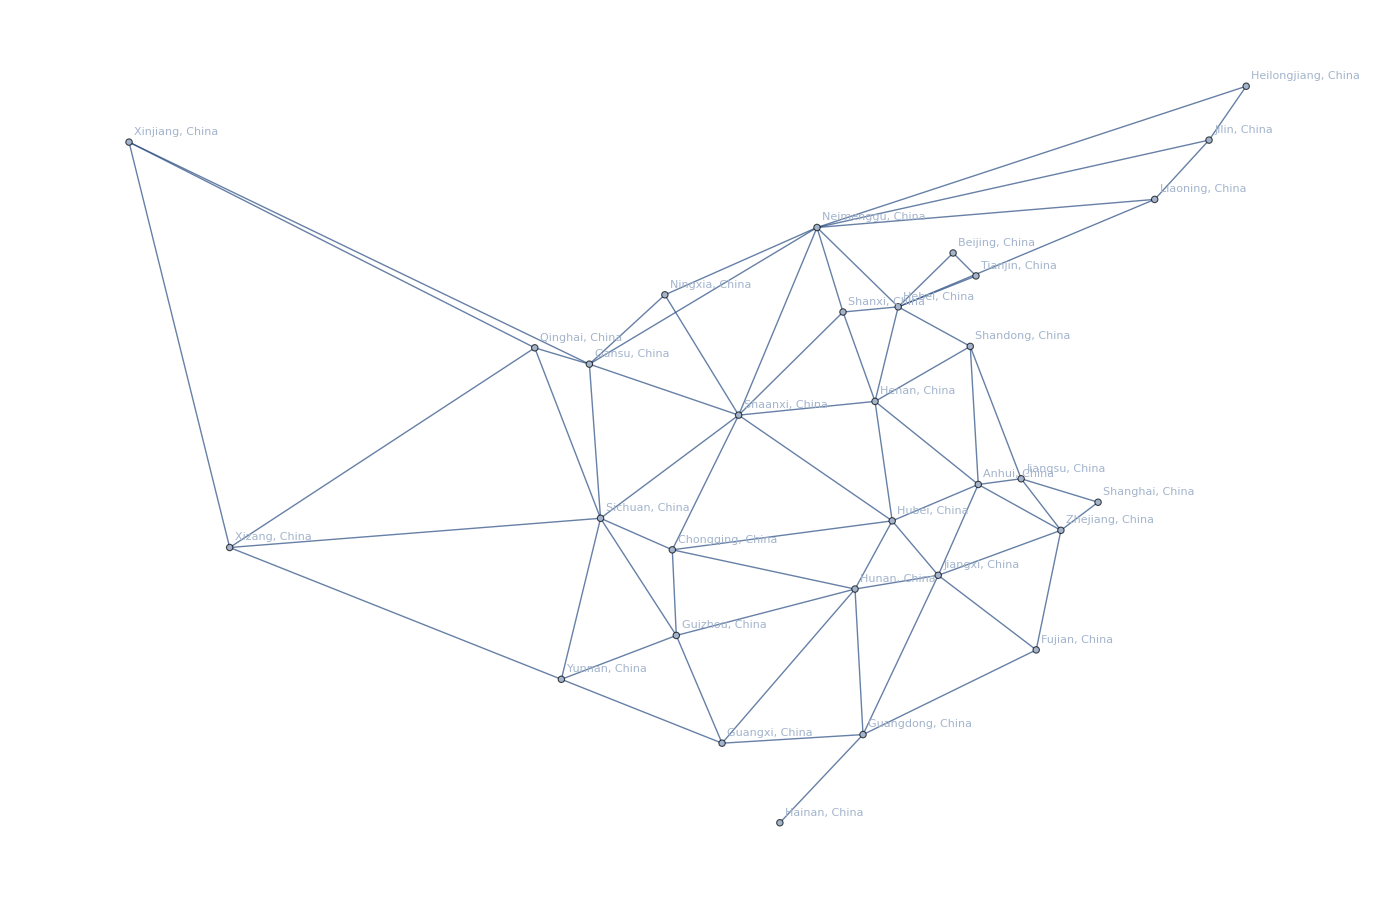

```mathematica
Graph[g,VertexCoordinates->coords,VertexLabels->"Name"]
```

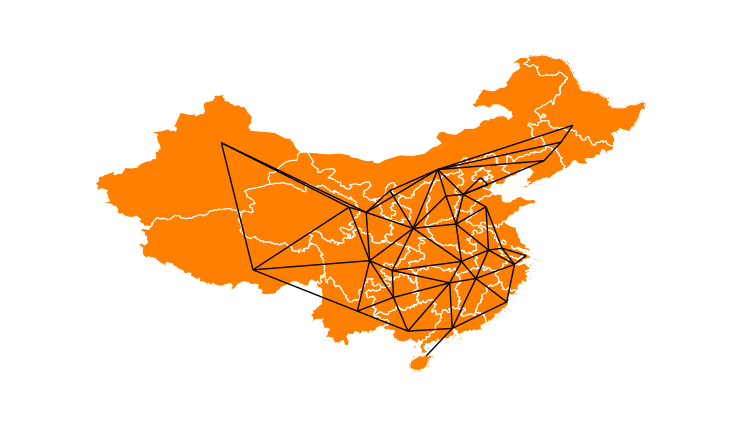

```mathematica
GeoGraphics[{
{GeoStyling[{EdgeForm[White],FaceForm[Orange]}],Map[Polygon,provinces]},
Map[Line[{Reverse[First[#][EntityProperty["AdministrativeDivision","CapitalCity"]][EntityProperty["City","Coordinates"]]],Reverse[Last[#][EntityProperty["AdministrativeDivision","CapitalCity"]][EntityProperty["City","Coordinates"]]]}]&,g]
},
GeoBackground->None]
```

#### x

```mathematica
Get["https://raw.githubusercontent.com/szhorvat/IGraphM/master/IGInstaller.m"]
```

The currently installed versions of IGraph/M are: {}

Installing IGraph/M is complete: PacletObject[…].

It can now be loaded using the command <<IGraphM`

```mathematica
<<"IGraphM`"
```

IGraph/M 0.3.113 (February 9, 2020)
Evaluate IGDocumentation[] to get started.

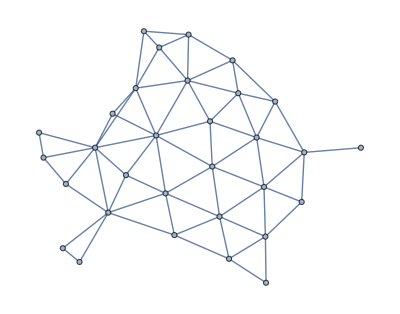

```mathematica
gg=Graph[g]
```

```mathematica
ts=IGSIRProcess[gg,{2,1}]
```

TimeSeries[…]

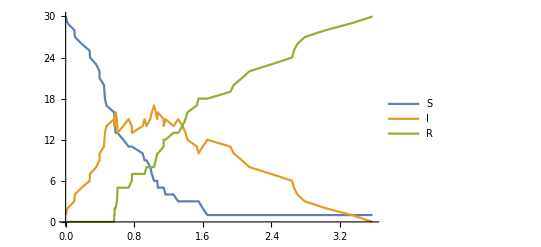

```mathematica
ListLinePlot[ts,PlotLegends->ts["ComponentNames"]]
```

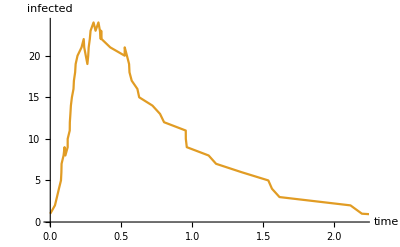

```mathematica
ListLinePlot[ts["PathComponent",2],
AxesLabel->{"time","infected"},PlotStyle->ColorData[97][2]]
```

```mathematica
ts[1.0]
```

{0.,8.75209,22.2479}

```mathematica
td=IGSIRProcess[gg,{5,1},100]
```

TemporalData[…]

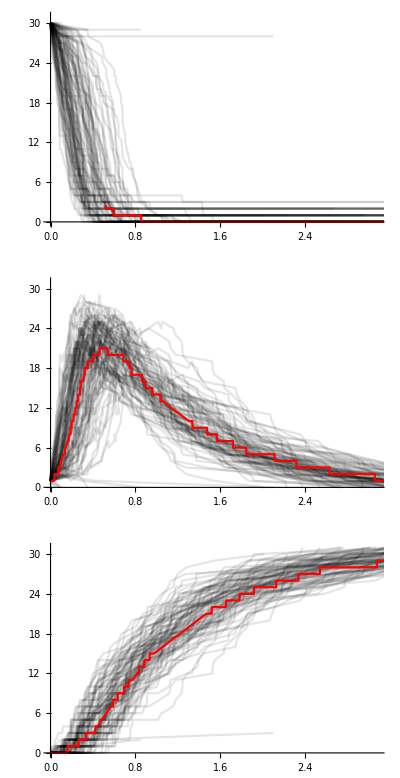

```mathematica
Show[
ListLinePlot[#,PlotStyle->GrayLevel[0,0.1],PlotRange->{0,VertexCount[gg]}],
Quiet@Plot[Median[#[t]],{t,0,4},PlotStyle->Red]
]&/@td["PathComponents"]//GraphicsColumn
```